#### Global Variables

```mathematica
prec=100;

Nmax = 100;

x = 20.0;

xmax = 20.0;
xmin = -20.0;
xsize = 100;
dx=(xmax-xmin)/(xsize-1);

Xvector = N[Range[xmin,xmax,dx],prec];
Nvector = Range[0,Nmax,1];
```

#### Wavefuntion_Wolfram_Mathematica_1

```mathematica
WavefunctionMathematica1[n_,x_,prec_]:=Module[{nPrec,xPrec,norm,H,wavefunction},
SetPrecision[n,prec];
SetPrecision[x,prec];
norm=(2^(-0.5*n))*(Gamma[n+1]^(-0.5))*(Pi^(-0.25));
H=HermiteH[n,x];
wavefunction=SetPrecision[norm*Exp[-0.5*x^2]*H,prec];
wavefunction];
```

#### Wavefuntion_Wolfram_Mathematica_2

```mathematica
WavefunctionMathematica2[n_,x_,prec_]:=Module[{wavefunction,xsize,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
wavefunction[[2]]=SetPrecision[(2 x wavefunction[[1]])/Sqrt[2],prec];
For[i=3,i<=n+1,i++,wavefunction[[i]]=2 x (wavefunction[[i-1]]/Sqrt[2 (i-1)])-Sqrt[(i-2)/(i-1)] wavefunction[[i-2]];];
wavefunction[[n+1]]];
```

#### Wavefuntion_Wolfram_Mathematica_3

```mathematica
WavefunctionMathematica3[n_,x_,prec_]:=Module[{wavefunction,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
For[i=1,i<=n,i++,
wavefunction[[i+1]]=
SetPrecision[2 x (wavefunction[[i]]/Sqrt[2 (i)])-
Sqrt[(i-1)/i] wavefunction[[i-1]],prec]];

wavefunction];
```

#### Tests

Single-Mode and Onedimensional speed test

Functionality Test Passed: True

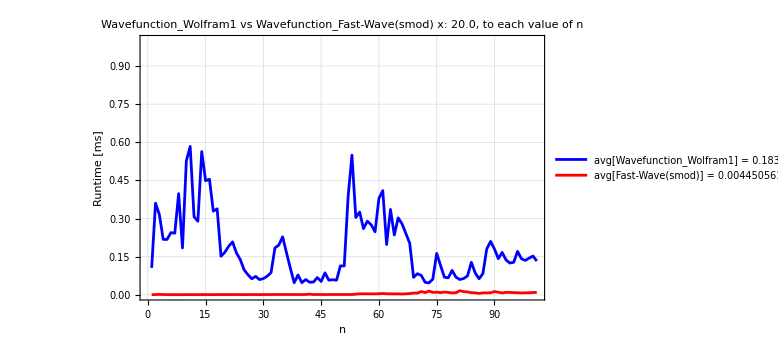

```mathematica
(*To use timeit.repeat in the Python is a option too*)

FastWaveSMODList=Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import timeit;N_max = 100;x = 20.0;[(timeit.timeit(lambda : wavefunction_smod(n, x) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSMODList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSMODList,
RepeatedTiming[WavefunctionMathematica1[i-1,x,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSMODList,FastWaveSMODList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod)",Bold,13],"\n",Style["x: 20.0, to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSMODList],20],TraditionalForm] <> " ms;" ,
" avg[Fast-Wave(smod)] = "<> ToString[SetPrecision[Mean[FastWaveSMODList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.0}}
]
```

#### Single-Mode and Onedimensional speed test (less_fast)

Functionality Test Passed: True

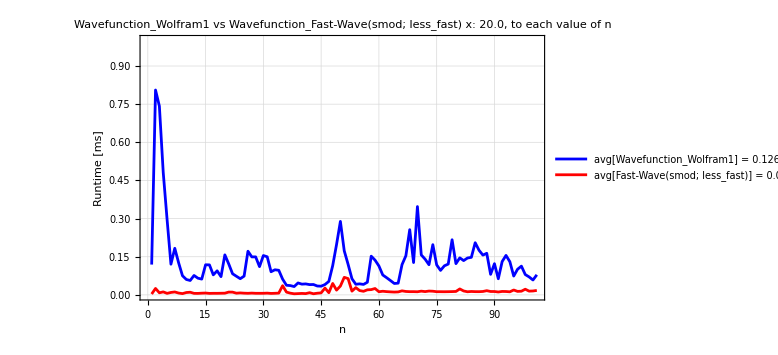

```mathematica
FastWaveSMODList=Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smod;import timeit;N_max = 100;x = 20.0;[(timeit.timeit(lambda : wavefunction_smod(n, x, more_fast=False) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSMODList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSMODList,
RepeatedTiming[WavefunctionMathematica1[i-1,x,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSMODList,FastWaveSMODList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smod; less_fast)",Bold,13],"\n",Style["x: 20.0, to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSMODList],20],TraditionalForm] <> " ms;" ,
" avg[Fast-Wave(smod; less_fast)] = "<> ToString[SetPrecision[Mean[FastWaveSMODList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.0}}
]
```

#### Single-Mode and Multidimensional speed test

Functionality Test Passed: True

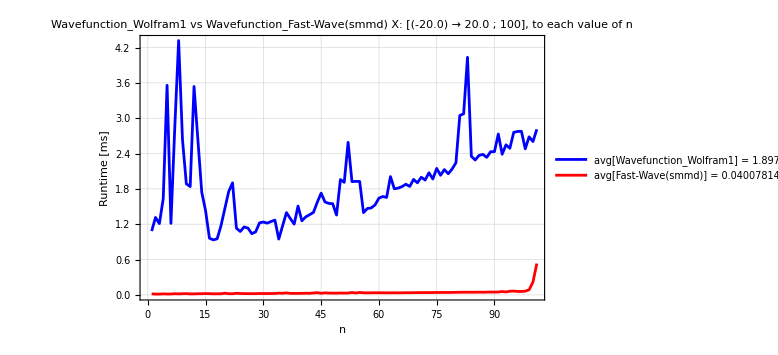

```mathematica
FastWaveSMMDList=Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smmd;import timeit;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[(timeit.timeit(lambda : wavefunction_smmd(n, X) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSMMDList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSMMDList,
RepeatedTiming[WavefunctionMathematica1[i-1,Xvector,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSMMDList,FastWaveSMMDList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smmd)",Bold,13],"\n",Style["X: [(-20.0) → 20.0 ; 100], to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSMMDList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(smmd)] = "<> ToString[SetPrecision[Mean[FastWaveSMMDList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```

#### Single-Mode and Multidimensional speed test (less_fast)

Functionality Test Passed: True

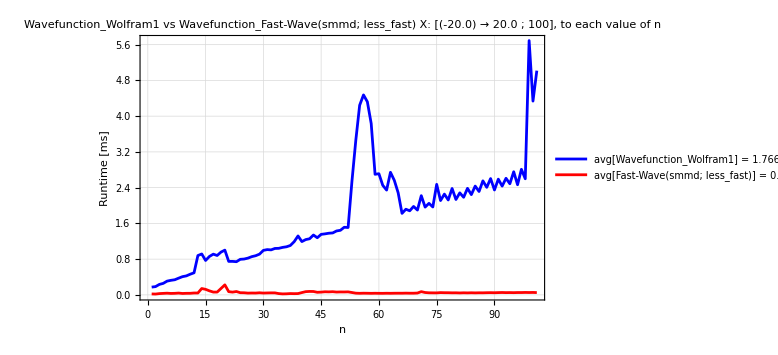

```mathematica
FastWaveSMMDList=Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_smmd;import timeit;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[(timeit.timeit(lambda : wavefunction_smmd(n, X, more_fast = False) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframSMMDList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframSMMDList,
RepeatedTiming[WavefunctionMathematica1[i-1,Xvector,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframSMMDList,FastWaveSMMDList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave(smmd; less_fast)",Bold,13],"\n",Style["X: [(-20.0) → 20.0 ; 100], to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram1] = " <>ToString[SetPrecision[Mean[WavefunctionWolframSMMDList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(smmd; less_fast)] = "<> ToString[SetPrecision[Mean[FastWaveSMMDList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```

#### Multi-Mode and Onedimensional speed test

Functionality Test Passed: True

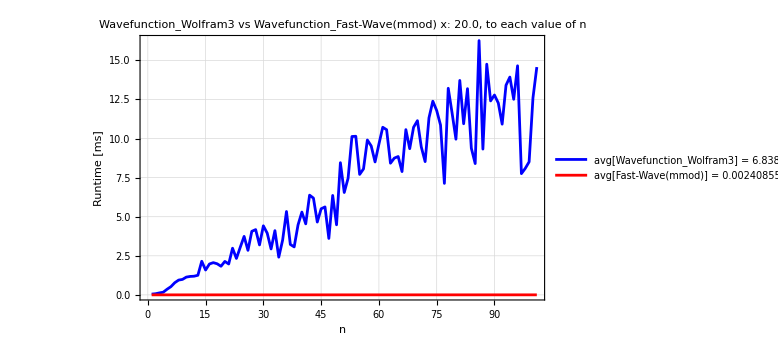

```mathematica
FastWaveMMODList=Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_mmod;import timeit;N_max = 100;x = 20.0;[(timeit.timeit(lambda : wavefunction_mmod(n, x) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframMMODList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframMMODList,
RepeatedTiming[WavefunctionMathematica3[i-1,x,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframMMODList,FastWaveMMODList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mmod)",Bold,13],"\n",Style["x: 20.0, to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram3] = " <>ToString[SetPrecision[Mean[WavefunctionWolframMMODList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(mmod)] = "<> ToString[SetPrecision[Mean[FastWaveMMODList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```

#### Multi-Mode and Multidimensional speed test

Functionality Test Passed: True

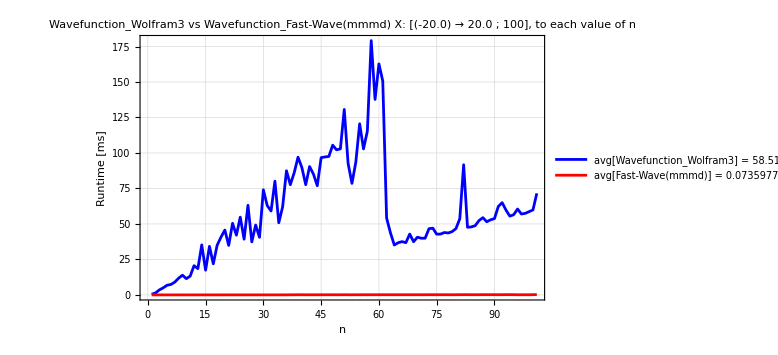

```mathematica
FastWaveMMMDList=Normal[ExternalEvaluate["Python",                      "from fast_wave.wavefunction import wavefunction_mmmd;import timeit;import numpy as np;N_max = 100;xmax = 20.0;xmin = -20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[(timeit.timeit(lambda : wavefunction_mmmd(n, X) , number=10000)/10000)*1000 for n in range(N_max+1)];"]];

WavefunctionWolframMMMDList = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionWolframMMMDList,
RepeatedTiming[WavefunctionMathematica3[i-1,Xvector,prec]][[1]]*1000];]

ListLinePlot[
{WavefunctionWolframMMMDList,FastWaveMMMDList},
PlotStyle->{Blue, Red},
Frame->True,
FrameLabel->{"n","Runtime [ms]"},
PlotLabel->Row[{Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mmmd)",Bold,13],"\n",Style["X: [(-20.0) → 20.0 ; 100], to each value of n \n",12]}],
GridLines->Automatic,
PlotLegends->Placed[{" avg[Wavefunction_Wolfram3] = " <>ToString[SetPrecision[Mean[WavefunctionWolframMMMDList],20],TraditionalForm] <> " ms",
" avg[Fast-Wave(mmmd)] = "<> ToString[SetPrecision[Mean[FastWaveMMMDList],20],TraditionalForm] <> " ms"},Below],
ImageSize->Large ]
```